# Solar geometry : latitude, day angle and solar declination

```mathematica
(* ::Subsection::*)(*Definition of site latitude*)(*Site latitude in radians.The reference location considered in this model is set to 37 degrees north.This parameter defines the observer position on Earth and directly affects the solar trajectory and all derived solar angles.*)
latitude=37 Degree;

(* ::Subsection::*)
(*Day angle and solar declination (Spencer model)*)

(*Daily angle beta(dn),also known as the day angle.This variable maps the day of the year (dn) into a periodic angular scale,representing the Earth's orbit around the Sun.*)
beta[dn_]:=2 Pi (dn-1)/365;


(*Solar declination delta(dn) computed using Spencer's Fourier-series approximation.This analytical expression provides a high-accuracy representation of the seasonal variation of the solar declination angle.The declination angle defines the tilt between the Earth's equatorial plane and the Sun-Earth direction,and it is a key input for computing solar elevation and azimuth angles.*)
delta[dn_]:=0.006918-0.399912 Cos[beta[dn]]+0.070257 Sin[beta[dn]]-0.006758 Cos[2 beta[dn]]+0.000907 Sin[2 beta[dn]]-0.002697 Cos[3 beta[dn]]+0.00148 Sin[3 beta[dn]];


(*Visualization of solar declination over the year.This plot illustrates the seasonal variation of the declination angle,ranging approximately between-23.44° and+23.44°.*)
Plot[{delta[dd]},{dd,1,365},FrameLabel->{"Day of year (dn)","δ [rad]"},Frame->True,PlotTheme->"Marketing",LabelStyle->Directive[Black,Bold,Large]]
```

-Graphics-

# Solar time and solar angles

```mathematica
(* ::Subsection::*)(*Hour angle and solar time*)(*Hour angle H (in radians) computed from the true solar time (TST,in hours).The hour angle represents the angular displacement of the Sun with respect to the local meridian.It is zero at solar noon,negative in the morning,and positive in the afternoon.The factor 15° per hour corresponds to the Earth's rotation rate.Subtracting 12 centers the system at solar noon.*)timeH[TST_]:=15 Degree (TST-12);

(* ::Subsection::*)
(*Solar elevation and zenith angles*)

(*Solar zenith angle Z (in radians).This is the angle between the local vertical direction and the solar direction.Note:This angle is NOT the solar azimuth.*)
zenith[dn_,TST_]:=ArcCos[Sin[latitude] Sin[delta[dn]]+Cos[latitude] Cos[delta[dn]] Cos[timeH[TST]]];

(*Solar elevation angle h (in radians).This is the angle between the solar direction and the horizontal plane.*)
h[dn_,TST_]:=ArcSin[Sin[latitude] Sin[delta[dn]]+Cos[latitude] Cos[delta[dn]] Cos[timeH[TST]]];

(* ::Subsection::*)
(*Geometric solar azimuth (model convention)*)

(*Solar azimuth in the geometric convention adopted for the mirror model.This is a signed angle in the horizontal xy-plane:-measured from the positive x-axis-counterclockwise-negative in the morning,positive in the afternoon This definition differs from standard solar azimuth formulations,but preserves continuity and is consistent with the geometric construction of the mirror surface.*)
azimuth[dn_,TST_]:=Module[{sx,sy},(*Horizontal projection of the solar direction*)sx=Sin[latitude] Cos[delta[dn]] Cos[timeH[TST]]-Cos[latitude] Sin[delta[dn]];
sy=Cos[delta[dn]] Sin[timeH[TST]];
(*Quadrant-aware angle*)ArcTan[sx,sy]];

(* ::Subsection::*)
(*Consistency check*)

(*Example day for validation*)
dn=160;

(*The zenith angle must satisfy:zenith=Pi/2-elevation*)
Plot[{zenith[dn,hora],Pi/2-h[dn,hora]},{hora,9,15},FrameLabel->{"Solar time [h]","Angle [rad]"},Frame->True,PlotTheme->"Marketing",PlotLegends->{"zenith","Pi/2 - elevation"},LabelStyle->Directive[Black,Bold,Large]]
```

-Graphics-

# Horizontal projection

### This block computes the horizontal projection of the solar direction for a selected day . The resulting curve represents the solar sweep in the xy - plane using the geometric convention adopted in this model . In this convention, the azimuth is not expressed in the standard astronomical reference frame, but as a signed geometric angle measured from the positive x - axis in the counterclockwise direction . This definition is the one used later to generate the parabolic sections and the three - dimensional mirror surface .

```mathematica
(* ::Subsection::*)(*Horizontal projection of the solar direction*)(*Horizontal x-component of the solar direction.Cos[h] gives the magnitude of the horizontal projection,while Cos[azimuth] gives its component along the x-axis.*)x[dn_,TST_]:=Cos[h[dn,TST]] Cos[azimuth[dn,TST]];

(*Horizontal y-component of the solar direction.Cos[h] gives the magnitude of the horizontal projection,while Sin[azimuth] gives its component along the y-axis.*)
y[dn_,TST_]:=Cos[h[dn,TST]] Sin[azimuth[dn,TST]];


(* ::Subsection::*)
(*Example of daily horizontal sweep*)

(*Example day and facade length used for visualization.*)
dn=170;
FacadeLength=30;

(*Normalization factor for the lateral excursion over the selected time interval.This avoids using a single endpoint as reference and keeps the sweep scaled to the facade width.*)
yNorm=Max[Abs@Table[y[dn,hora],{hora,12-3,12+3,0.01}]];

(*Daily horizontal solar sweep in the adopted geometric convention.The x-component is kept in its natural normalized form,whereas the y-component is scaled to the facade width in order to visualize the region where the distributed reactor is placed.*)
dataXY=Table[{x[dn,hora],(FacadeLength/2) y[dn,hora]/yNorm,0},{hora,12-3,12+3,0.01}];

(*3D visualization of the horizontal solar path.Although the curve lies in the plane z=0,ListPointPlot3D is used to maintain consistency with the later 3D representation of the mirror surface and focal trajectory.*)
horizontalSweep=ListPointPlot3D[dataXY,AxesLabel->{"x [m]","y [m]","z [m]"},PlotLabel->"Horizontal solar sweep in the model reference frame",PlotTheme->"Marketing",LabelStyle->Directive[Black,Bold],AspectRatio->1]
```

-Graphics3D-

# Local parabolic profile driven by solar elevation

### This section illustrates how the local parabolic cross - section of the mirror evolves throughout the day as a function of the solar elevation . The purpose of this block is mainly interpretative : through static examples and animations, it helps to understand how each parabola tilts, rises, and descends as the Sun moves from morning to afternoon . In this stage, only the vertical plane (xz - plane) is considered . The horizontal azimuthal sweep will be introduced later in the full three - dimensional construction of the mirror surface . Mirror profile for a fixed day.This section illustrates how each local parabolic cross-section is generated in the vertical plane as a function of solar time.The local profile is controlled by the solar zenith angle,whereas the horizontal azimuthal sweep is introduced later in the full 3D construction of the mirror surface.

```mathematica
(* ::Subsection::*)(*Reference day and geometric parameters*)(*Selected day of the year.This example uses day 160,corresponding approximately to early June in a non-leap year.*)dn=160;

(*Focal length of the parabolic mirror (in meters).*)
f=1;

(* ::Subsection::*)
(*Local orientation of the parabolic profile*)

(*Local rotation angle of the parabolic section.The profile is oriented according to the solar zenith angle,which defines the inclination of the incoming solar rays in the vertical plane.*)
thetaLocal[TST_]:=zenith[dn,TST];


(* ::Subsection::*)
(*Parametric definition of the parabolic profile*)

(*Local x-coordinate of the rotated parabola.The expression corresponds to a standard parabola rotated by the zenith angle.*)
xLocal[t_,TST_]:=t Cos[thetaLocal[TST]]-(t^2/(4 f)) Sin[thetaLocal[TST]];

(*Local z-coordinate of the rotated parabola.*)
zLocal[t_,TST_]:=t Sin[thetaLocal[TST]]+(t^2/(4 f)) Cos[thetaLocal[TST]];

(* ::Subsection::*)
(*Focal point associated with the solar elevation*)

(*The focal point follows the solar elevation angle.Its position shifts vertically throughout the day as the Sun rises and sets.*)
fxLocal[TST_]:=-f Cos[h[dn,TST]];
fzLocal[TST_]:=f Sin[h[dn,TST]];

(* ::Subsection::*)
(*Static example:single solar time*)

(*Example of the parabolic profile at a fixed solar time.This allows visualizing the geometry of a single mirror section and its corresponding focal point.*)
exampleProfile=Show[ParametricPlot[{xLocal[t,10],zLocal[t,10]},{t,-4,4},PlotStyle->Thick,Frame->True,FrameLabel->{"x [m]","z [m]"},PlotLabel->"Local parabolic mirror profile",LabelStyle->Directive[Black,Bold]],ListPlot[{{fxLocal[10],fzLocal[10]}},PlotStyle->{Red,PointSize[Large]}]];
```

```mathematica
(* ::Subsection::*)(*Animation of the daily evolution of the parabolic profile*)(*This animation shows how the parabolic profile continuously changes throughout the day.As the solar elevation increases (morning to noon),the parabola tilts upward and its focal point rises.After solar noon,the process reverses:the parabola descends and the focal point lowers.This dynamic behavior is the basis for constructing the full mirror surface as an envelope of time-dependent parabolic sections.*)Animate[Show[ParametricPlot[{xLocal[t,TST],zLocal[t,TST]},{t,-4,4},PlotStyle->Thick,Frame->True,FrameLabel->{"x [m]","z [m]"}],ListPlot[{{fxLocal[TST],fzLocal[TST]}},PlotStyle->{Red,PointSize[Large]}]],{TST,9,15,Appearance->"Labeled"},AnimationRunning->False]
```

# Parametric construction of the mirror surface

### This section introduces the full parametric construction of the mirror surface . The mirror is generated as a collection of local parabolic sections defined in the vertical plane (xz - plane), which are subsequently positioned in space through rigid transformations . Each section is : -oriented according to the solar zenith angle (vertical tilt), -rotated according to the geometric solar azimuth (horizontal sweep), -translated along the horizontal solar trajectory . The combination of these operations produces the complete three - dimensional geometry of the mirror as an envelope of time - dependent parabolic profiles .

```mathematica
(* ::Subsection::*)(*Rigid transformation in 3D space*)(*Rigid transformation of a 3D point set:-first,a rotation around the z-axis,-then,a translation in the xy-plane.This transformation is essential to correctly place each local parabolic section in the global coordinate system,assigning both its azimuthal orientation and its horizontal position along the solar trajectory.*)TransformCurve[points_List,angle_,dx_,dy_]:=Module[{rotationMatrix,rotatedPoints},(*Rotation matrix around the z-axis*)rotationMatrix={{Cos[angle],-Sin[angle],0},{Sin[angle],Cos[angle],0},{0,0,1}};
(*Apply rotation*)rotatedPoints=(rotationMatrix.#)&/@points;
(*Apply translation in the xy-plane*)(#+{dx,dy,0})&/@rotatedPoints];
```

```mathematica
(* ::Subsection::*)(*Local parabolic profile (vertical plane)*)(*Focal length of the parabolic cross-section (in meters).*)
f=1;

(*Local x-coordinate of the parabolic profile.The parabola is defined in the vertical plane and rotated according to the solar zenith angle,which determines the inclination of the incident solar rays.*)
xref[dn_,TST_,t_]:=t Cos[zenith[dn,TST]]-(t^2/(4 f)) Sin[zenith[dn,TST]];

(*Local z-coordinate of the parabolic profile.*)
zref[dn_,TST_,t_]:=t Sin[zenith[dn,TST]]+(t^2/(4 f)) Cos[zenith[dn,TST]];
```

```mathematica
(* ::Subsection::*)(*Focal trajectory*)(*Horizontal coordinate of the focal point.The focal point shifts horizontally according to the solar elevation.*)fx[dn_,TST_]:=-f Cos[h[dn,TST]];

(*Vertical coordinate of the focal point.The focal point rises and descends following the solar elevation.*)
fz[dn_,TST_]:=f Sin[h[dn,TST]];
```

```mathematica
(* ::Subsection::*)(*Horizontal solar projection (geometric azimuth)*)(*Horizontal x-component of the solar direction.The projection is defined using the geometric azimuth introduced previously,ensuring consistency with the model reference frame.*)
x[dn_,TST_]:=Cos[h[dn,TST]] Cos[azimuth[dn,TST]];

(*Horizontal y-component of the solar direction.*)
y[dn_,TST_]:=Cos[h[dn,TST]] Sin[azimuth[dn,TST]];
```

```mathematica
(* ::Subsection::*)(*Geometric scaling parameters*)(*Facade length (in meters).This parameter defines the physical extent of the mirror system in the horizontal direction and is used later to scale the solar sweep.*)FacadeLength=30;
```

## Generation of the mirror surface and focal trajectory for selected days

#### This block defines a reusable function that generates both the mirror surface and the associated focal trajectory for any selected day of the year.The construction is performed by sweeping the true solar time over the operating interval.For each solar time:-a local parabolic section is generated in the xz-plane,-the corresponding focal point is computed,-both are rotated according to the geometric azimuth,-and translated along the horizontal solar sweep.The output is stored as an association with two components:"Surface",containing the collection of transformed parabolic sections,and "Focus",containing the corresponding transformed focal points.This modular construction makes it possible to compare mirror geometries generated for different days under identical sampling conditions.

```mathematica
(* ::Subsection::*)(*Reusable generator for the mirror surface and focal trajectory*)(*GenerateSurfaceAndFocus[dn] constructs the mirror surface and the corresponding focal trajectory for a given day of the year.Input:-dn:day number of the year Output:-an association with two entries:"Surface"->collection of transformed parabolic sections "Focus"->collection of transformed focal points*)GenerateSurfaceAndFocus[dn_]:=Module[{j=0,yNormLocal,data,focus},(*Normalization factor for the lateral displacement over the full operating interval of the selected day.This ensures that the horizontal sweep is consistently scaled.*)
yNormLocal=Max[Abs@Table[y[dn,TST],{TST,12-3,12+3,0.01}]];
(*Sweep the true solar time over the selected operating window.*)
For[TST=12-3,TST<=12+3,TST+=0.05,j=j+1;
(*Initialize storage for the current parabolic section and focal point.*)
data[j]={};
focus[j]={};
(*Generate the local parabolic profile in the xz-plane by sweeping the parabola parameter t.*)For[i=-600,i<=600,i++,t=i/200;
data[j]=Append[data[j],{xref[dn,TST,t],0,zref[dn,TST,t]}];];
(*Local focal point before the rigid transformation.*)
focus[j]={{fx[dn,TST],0,fz[dn,TST]}};
(*Apply the rigid transformation to the focal point:-rotation by the opposite of the geometric azimuth,-translation along the horizontal solar trajectory.*)focus[j]=TransformCurve[focus[j],-azimuth[dn,TST],x[dn,TST],FacadeLength/2*y[dn,TST]/yNormLocal];
(*Apply the same rigid transformation to the full parabolic section.*)data[j]=TransformCurve[data[j],-azimuth[dn,TST],x[dn,TST],FacadeLength/2*y[dn,TST]/yNormLocal];];
(*Return both the mirror surface and the focal trajectory as an association.*)<|"Surface"->Table[data[k],{k,1,j}],"Focus"->Table[focus[k],{k,1,j}]|>];
```

```mathematica
(* ::Subsection::*)(*Generation of mirror surfaces for two representative summer days*)(*Two representative summer days are considered in order to compare the resulting mirror geometries and focal trajectories.Day 170 is used as a reference summer day.Day 176 is introduced as a nearby operating day to evaluate whether the mirror geometry remains practically unchanged within the selected summer interval.*)day170=GenerateSurfaceAndFocus[170];
day176=GenerateSurfaceAndFocus[176];
```

```mathematica
(* ::Subsection::*)(*Extraction of surfaces and focal trajectories*)(*Mirror surface and focal trajectory for day 170.*)SurfacesDay170=day170["Surface"];
ReactorDay170=day170["Focus"];

(*Mirror surface and focal trajectory for day 176.*)
SurfacesDay176=day176["Surface"];
ReactorDay176=day176["Focus"];
```

#### At this stage, the mirror surface is represented as a discrete set of transformed parabolic sections . In later steps, this point cloud can be visualized, interpolated, or exported for fabrication and simulation .

```mathematica
rangoDay170=Show[ListPointPlot3D[SurfacesDay170,AxesLabel->{"y [m]","x [m]","z [m]"},LabelStyle->Directive[Black,Bold,Large]],ListPointPlot3D[ReactorDay170,AxesLabel->{"y [m]","x [m]","z [m]"},LabelStyle->Directive[Black,Bold,Large]]]
```

-Graphics3D-

```mathematica
rangoDay176=Show[ListPointPlot3D[SurfacesDay176,AxesLabel->{"y [m]","x [m]","z [m]"},LabelStyle->Directive[Black,Bold,Large]],ListPointPlot3D[ReactorDay176,AxesLabel->{"y [m]","x [m]","z [m]"},LabelStyle->Directive[Black,Bold,Large]]]
```

-Graphics3D-

# Quantitative comparison between day 170 and day 176

```mathematica
(*Visual comparison of the mirror surfaces and focal trajectories corresponding to day 170 and day 176. Both datasets are plotted simultaneously in order to qualitatively assess the overlap between the two geometries.This visualization provides an intuitive confirmation that the surfaces are nearly indistinguishable within the selected summer operating interval.However,visual inspection alone is not sufficient to quantify the differences.For this reason,a detailed pointwise numerical comparison is performed in the following section.*)
Show[rangoDay170,rangoDay176]
```

-Graphics3D-

```mathematica
(* ::Section::*)(*Quantitative comparison between day 170 and day 176*)(*This block compares the mirror surfaces and focal trajectories obtained for day 170 and day 176. Since both surfaces are generated with the same parameter sampling in solar time and in the local parabola parameter t,a point-to-point comparison can be performed directly.The goal is to quantify how close both parametric surfaces are over the selected summer operating interval.*)(*Pointwise Euclidean distances between both mirror surfaces*)surfacePointDistances=MapThread[EuclideanDistance,{Flatten[SurfacesDay170,1],Flatten[SurfacesDay176,1]}];

(*Pointwise Euclidean distances between both focal trajectories*)
focusPointDistances=MapThread[EuclideanDistance,{Flatten[ReactorDay170,1],Flatten[ReactorDay176,1]}];

(*Summary statistics for the mirror surface*)
surfaceMaxError=Max[surfacePointDistances];
surfaceMeanError=Mean[surfacePointDistances];
surfaceRMSError=Sqrt[Mean[surfacePointDistances^2]];

(*Summary statistics for the focal trajectory*)
focusMaxError=Max[focusPointDistances];
focusMeanError=Mean[focusPointDistances];
focusRMSError=Sqrt[Mean[focusPointDistances^2]];

comparisonSummary={"Surface max error [m]"->surfaceMaxError,"Surface mean error [m]"->surfaceMeanError,"Surface RMS error [m]"->surfaceRMSError,"Focus max error [m]"->focusMaxError,"Focus mean error [m]"->focusMeanError,"Focus RMS error [m]"->focusRMSError}
```

{Surface max error [m]→0.0000505361,Surface mean error [m]→0.000018596,Surface RMS error [m]→0.0000212276,Focus max error [m]→3.11953×10^-6,Focus mean error [m]→2.25404×10^-6,Focus RMS error [m]→2.29807×10^-6}

```mathematica
relativeComparisonSummary={"Surface max error / FacadeLength"->surfaceMaxError/FacadeLength,"Surface RMS error / FacadeLength"->surfaceRMSError/FacadeLength,"Focus max error / FacadeLength"->focusMaxError/FacadeLength,"Focus RMS error / FacadeLength"->focusRMSError/FacadeLength}
```

{Surface max error / FacadeLength→1.68454×10^-6,Surface RMS error / FacadeLength→7.07587×10^-7,Focus max error / FacadeLength→1.03984×10^-7,Focus RMS error / FacadeLength→7.66023×10^-8}

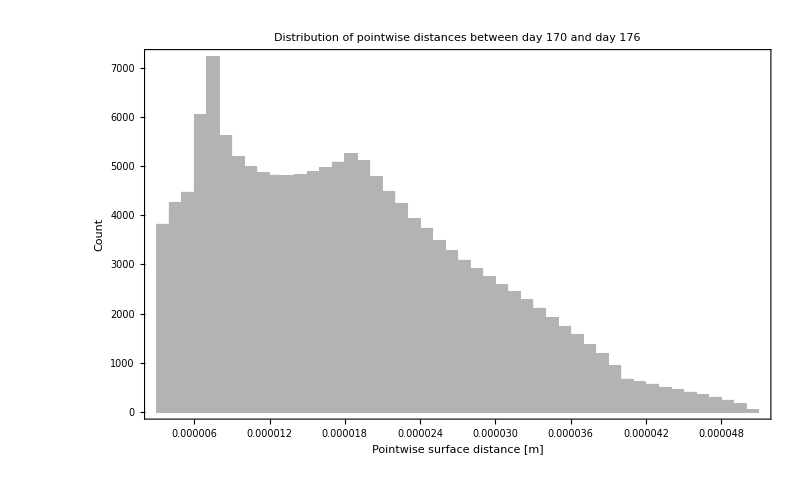

```mathematica
Histogram[surfacePointDistances,40,Frame->True,FrameLabel->{"Pointwise surface distance [m]","Count"},PlotLabel->"Distribution of pointwise distances between day 170 and day 176",PlotTheme->"Monochrome",LabelStyle->Directive[Black,Bold]]
```

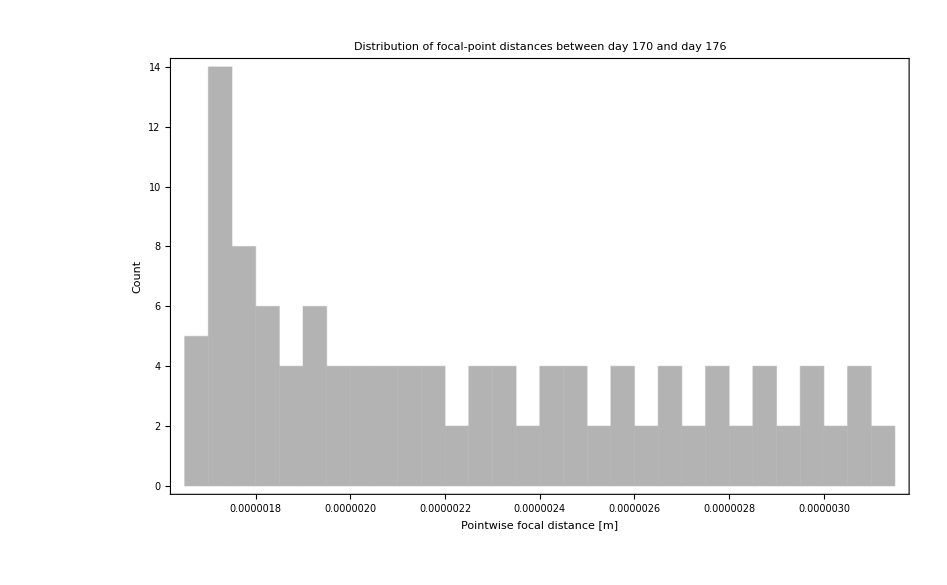

```mathematica
Histogram[focusPointDistances,30,Frame->True,FrameLabel->{"Pointwise focal distance [m]","Count"},PlotLabel->"Distribution of focal-point distances between day 170 and day 176",PlotTheme->"Monochrome",LabelStyle->Directive[Black,Bold]]
```

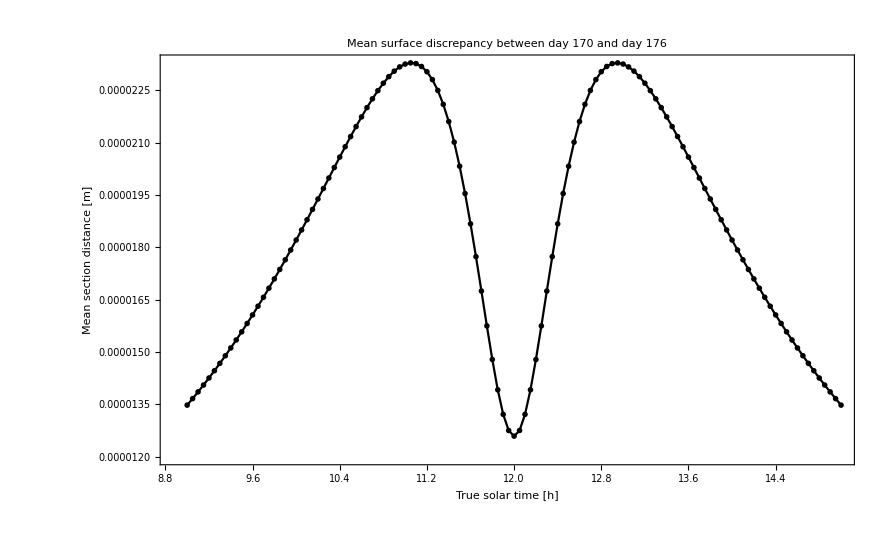

```mathematica
(*Distances section by section,one value per TST*)sectionErrors=Table[Mean[MapThread[EuclideanDistance,{SurfacesDay170[[k]],SurfacesDay176[[k]]}]],{k,1,Length[SurfacesDay170]}];

tstValues=Range[12-3,12+3,0.05];

ListLinePlot[Transpose[{tstValues,sectionErrors}],Frame->True,FrameLabel->{"True solar time [h]","Mean section distance [m]"},PlotLabel->"Mean surface discrepancy between day 170 and day 176",PlotTheme->"Monochrome",LabelStyle->Directive[Black,Bold]]
```

#### The overlap between the surfaces generated for day 170 and day 176 can be inspected visually,but a quantitative comparison is more informative.Since both surfaces are generated using the same parameter sampling in solar time and in the parabola parameter t,a pointwise comparison can be performed directly.This makes it possible to evaluate the maximum,mean,and RMS discrepancy between both mirror surfaces and between their corresponding focal trajectories.If these discrepancies remain small compared with the characteristic dimensions of the system,both days can be considered geometrically equivalent for practical design purposes.